# Eigenvalue Stability Test

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]]
```

C:\Users\natha\Documents\School\Research\Hirschmann\HirschmannGroupBYU\Notes\MathematicaNotebooks

# A4 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["P4_interiorCoeffs.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs0.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs1.mx"]]
ParallelEvaluate[Get["P4_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1,1}

Kernel 2 working on {1,1,2}

Kernel 3 working on {1,2,1}

Kernel 4 working on {1,2,2}

Kernel 1 working on {1,3,1}

Kernel 2 working on {1,3,2}

Kernel 3 working on {1,4,1}

Kernel 4 working on {1,4,2}

Kernel 1 working on {1,5,1}

Kernel 4 working on {1,5,2}

Kernel 2 working on {2,1,1}

Kernel 3 working on {2,1,2}

Kernel 3 working on {2,2,1}

Kernel 1 working on {2,2,2}

Kernel 4 working on {2,3,1}

Kernel 2 working on {2,3,2}

Kernel 3 working on {2,4,1}

Kernel 1 working on {2,4,2}

Kernel 4 working on {2,5,1}

Kernel 2 working on {2,5,2}

Kernel 3 working on {3,1,1}

Kernel 4 working on {3,1,2}

Kernel 1 working on {3,2,1}

Kernel 2 working on {3,2,2}

Kernel 1 working on {3,3,1}

Kernel 3 working on {3,3,2}

Kernel 4 working on {3,4,1}

Kernel 2 working on {3,4,2}

Kernel 3 working on {3,5,1}

Kernel 1 working on {3,5,2}

Kernel 4 working on {4,1,1}

Kernel 2 working on {4,1,2}

Kernel 3 working on {4,2,1}

Kernel 1 working on {4,2,2}

Kernel 4 working on {4,3,1}

Kernel 2 working on {4,3,2}

Kernel 3 working on {4,4,1}

Kernel 1 working on {4,4,2}

Kernel 4 working on {4,5,1}

Kernel 2 working on {4,5,2}

Kernel 3 working on {5,1,1}

Kernel 1 working on {5,1,2}

Kernel 4 working on {5,2,1}

Kernel 2 working on {5,2,2}

Kernel 3 working on {5,3,1}

Kernel 4 working on {5,3,2}

Kernel 1 working on {5,4,1}

Kernel 2 working on {5,4,2}

Kernel 3 working on {5,5,1}

Kernel 1 working on {5,5,2}

{{{{{0.87,0.69,0.2},0.00370991},{{1.89,0.69,0.2},0.0111186}},{{{0.87,0.99,0.2},0.00217669},{{1.89,0.99,0.2},0.00742813}},{{{0.87,1.65,0.2},0.00686492},{{1.89,1.65,0.2},0.00409089}},{{{0.87,1.95,0.2},0.00944871},{{1.89,1.95,0.2},0.00658153}},{{{0.87,2.13,0.2},0.016068},{{1.89,2.13,0.2},0.00445062}}},{{{{0.87,0.69,0.63},0.00528961},{{1.89,0.69,0.63},0.0104879}},{{{0.87,0.99,0.63},0.00135212},{{1.89,0.99,0.63},0.00883387}},{{{0.87,1.65,0.63},0.00968873},{{1.89,1.65,0.63},0.0075007}},{{{0.87,1.95,0.63},0.0100095},{{1.89,1.95,0.63},0.00968781}},{{{0.87,2.13,0.63},0.0101971},{{1.89,2.13,0.63},0.00751622}}},{{{{0.87,0.69,1.05},0.0031788},{{1.89,0.69,1.05},0.0100769}},{{{0.87,0.99,1.05},0.00176513},{{1.89,0.99,1.05},0.00704724}},{{{0.87,1.65,1.05},0.00666026},{{1.89,1.65,1.05},-7.48025×10^-6}},{{{0.87,1.95,1.05},0.00943599},{{1.89,1.95,1.05},0.00553514}},{{{0.87,2.13,1.05},0.0152244},{{1.89,2.13,1.05},0.00139321}}},{{{{0.87,0.69,1.14},0.00292866},{{1.89,0.69,1.14},0.00978143}},{{{0.87,0.99,1.14},0.00146102},{{1.89,0.99,1.14},0.0069323}},{{{0.87,1.65,1.14},0.00667723},{{1.89,1.65,1.14},-0.0000116672}},{{{0.87,1.95,1.14},0.00948553},{{1.89,1.95,1.14},0.00563738}},{{{0.87,2.13,1.14},0.0139563},{{1.89,2.13,1.14},0.00208916}}},{{{{0.87,0.69,1.62},0.00808822},{{1.89,0.69,1.62},0.0083357}},{{{0.87,0.99,1.62},0.100829},{{1.89,0.99,1.62},0.00893766}},{{{0.87,1.65,1.62},0.00511377},{{1.89,1.65,1.62},0.00375924}},{{{0.87,1.95,1.62},0.0132883},{{1.89,1.95,1.62},0.00542204}},{{{0.87,2.13,1.62},0.00806977},{{1.89,2.13,1.62},0.00183651}}}}

```mathematica
DumpSave["A4_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A4_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

# C4 Scheme - try this next

## a)

# B4 Scheme - could be interesting

## a)

# A6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat1List={(*1*)0.51,(*2*)1.38,(*3*)1.92,(*4*)2.52,(*5*)3.39};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["A6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs1.mx"]]
ParallelEvaluate[Get["A6_bdCoeffs2.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«1 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]]},Max[Re[eigs]]},

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1,1}

Kernel 2 working on {1,1,2}

Kernel 3 working on {1,1,3}

Kernel 4 working on {1,1,4}

Kernel 2 working on {1,2,1}

Kernel 4 working on {1,2,2}

Kernel 3 working on {1,2,3}

Kernel 1 working on {1,2,4}

Kernel 3 working on {1,3,1}

Kernel 1 working on {1,3,2}

Kernel 4 working on {1,3,3}

Kernel 2 working on {1,3,4}

Kernel 2 working on {1,4,1}

Kernel 3 working on {1,4,2}

Kernel 4 working on {1,4,3}

Kernel 1 working on {1,4,4}

Kernel 2 working on {1,5,1}

Kernel 1 working on {1,5,2}

Kernel 3 working on {1,5,3}

Kernel 4 working on {1,5,4}

Kernel 1 working on {2,1,1}

Kernel 4 working on {2,1,2}

Kernel 2 working on {2,1,3}

Kernel 3 working on {2,1,4}

Kernel 4 working on {2,2,1}

Kernel 1 working on {2,2,2}

Kernel 2 working on {2,2,3}

Kernel 3 working on {2,2,4}

Kernel 4 working on {2,3,1}

Kernel 3 working on {2,3,2}

Kernel 1 working on {2,3,3}

Kernel 2 working on {2,3,4}

Kernel 4 working on {2,4,1}

Kernel 3 working on {2,4,2}

Kernel 1 working on {2,4,3}

Kernel 2 working on {2,4,4}

Kernel 4 working on {2,5,1}

Kernel 3 working on {2,5,2}

Kernel 1 working on {2,5,3}

Kernel 2 working on {2,5,4}

Kernel 4 working on {3,1,1}

Kernel 3 working on {3,1,2}

Kernel 1 working on {3,1,3}

Kernel 2 working on {3,1,4}

Kernel 4 working on {3,2,1}

Kernel 3 working on {3,2,2}

Kernel 1 working on {3,2,3}

Kernel 2 working on {3,2,4}

Kernel 4 working on {3,3,1}

Kernel 3 working on {3,3,2}

Kernel 1 working on {3,3,3}

Kernel 2 working on {3,3,4}

Kernel 4 working on {3,4,1}

Kernel 3 working on {3,4,2}

Kernel 2 working on {3,4,3}

Kernel 1 working on {3,4,4}

Kernel 4 working on {3,5,1}

Kernel 3 working on {3,5,2}

Kernel 2 working on {3,5,3}

Kernel 1 working on {3,5,4}

Kernel 3 working on {4,1,1}

Kernel 4 working on {4,1,2}

Kernel 2 working on {4,1,3}

Kernel 1 working on {4,1,4}

Kernel 3 working on {4,2,1}

Kernel 4 working on {4,2,2}

Kernel 2 working on {4,2,3}

Kernel 1 working on {4,2,4}

Kernel 3 working on {4,3,1}

Kernel 4 working on {4,3,2}

Kernel 2 working on {4,3,3}

Kernel 1 working on {4,3,4}

Kernel 3 working on {4,4,1}

Kernel 4 working on {4,4,2}

Kernel 2 working on {4,4,3}

Kernel 1 working on {4,4,4}

Kernel 3 working on {4,5,1}

Kernel 4 working on {4,5,2}

Kernel 2 working on {4,5,3}

Kernel 1 working on {4,5,4}

Kernel 3 working on {5,1,1}

Kernel 4 working on {5,1,2}

Kernel 2 working on {5,1,3}

Kernel 1 working on {5,1,4}

Kernel 3 working on {5,2,1}

Kernel 4 working on {5,2,2}

Kernel 2 working on {5,2,3}

Kernel 1 working on {5,2,4}

Kernel 3 working on {5,3,1}

Kernel 4 working on {5,3,2}

Kernel 2 working on {5,3,3}

Kernel 1 working on {5,3,4}

Kernel 3 working on {5,4,1}

Kernel 4 working on {5,4,2}

Kernel 2 working on {5,4,3}

Kernel 1 working on {5,4,4}

Kernel 3 working on {5,5,1}

Kernel 4 working on {5,5,2}

Kernel 2 working on {5,5,3}

Kernel 1 working on {5,5,4}

Kernel 4 working on {6,1,1}

Kernel 2 working on {6,1,2}

Kernel 3 working on {6,1,3}

Kernel 1 working on {6,1,4}

Kernel 4 working on {6,2,1}

Kernel 3 working on {6,2,2}

Kernel 2 working on {6,2,3}

Kernel 1 working on {6,2,4}

Kernel 2 working on {6,3,1}

Kernel 4 working on {6,3,2}

Kernel 1 working on {6,3,3}

Kernel 3 working on {6,3,4}

Kernel 2 working on {6,4,1}

Kernel 3 working on {6,4,2}

Kernel 4 working on {6,4,3}

Kernel 1 working on {6,4,4}

Kernel 2 working on {6,5,1}

Kernel 1 working on {6,5,2}

Kernel 3 working on {6,5,3}

Kernel 4 working on {6,5,4}

{{{{{1.5,0.51,0.9},0.163213},{{1.59,0.51,0.9},0.164309},{{3.12,0.51,0.9},0.286926},{{3.27,0.51,0.9},0.268744}},{{{1.5,1.38,0.9},0.130183},{{1.59,1.38,0.9},0.146124},{{3.12,1.38,0.9},0.131061},{{3.27,1.38,0.9},0.0981036}},{{{1.5,1.92,0.9},0.167367},{{1.59,1.92,0.9},0.166212},{{3.12,1.92,0.9},0.222522},{{3.27,1.92,0.9},0.297685}},{{{1.5,2.52,0.9},0.604258},{{1.59,2.52,0.9},0.196009},{{3.12,2.52,0.9},0.308647},{{3.27,2.52,0.9},0.223066}},{{{1.5,3.39,0.9},0.233703},{{1.59,3.39,0.9},0.202005},{{3.12,3.39,0.9},0.305245},{{3.27,3.39,0.9},0.238121}}},{{{{1.5,0.51,1.41},0.188841},{{1.59,0.51,1.41},0.197005},{{3.12,0.51,1.41},4.50976},{{3.27,0.51,1.41},2.92938}},{{{1.5,1.38,1.41},0.128041},{{1.59,1.38,1.41},0.143359},{{3.12,1.38,1.41},0.12328},{{3.27,1.38,1.41},0.101929}},{{{1.5,1.92,1.41},0.19472},{{1.59,1.92,1.41},0.198727},{{3.12,1.92,1.41},0.360402},{{3.27,1.92,1.41},0.91819}},{{{1.5,2.52,1.41},0.151257},{{1.59,2.52,1.41},0.16602},{{3.12,2.52,1.41},0.182413},{{3.27,2.52,1.41},0.0853158}},{{{1.5,3.39,1.41},0.268361},{{1.59,3.39,1.41},0.248729},{{3.12,3.39,1.41},0.38398},{{3.27,3.39,1.41},0.0863432}}},{{{{1.5,0.51,2.25},0.16751},{{1.59,0.51,2.25},0.16913},{{3.12,0.51,2.25},0.288239},{{3.27,0.51,2.25},0.270927}},{{{1.5,1.38,2.25},0.156635},{{1.59,1.38,2.25},0.165515},{{3.12,1.38,2.25},0.192256},{{3.27,1.38,2.25},0.56599}},{{{1.5,1.92,2.25},0.170881},{{1.59,1.92,2.25},0.170228},{{3.12,1.92,2.25},0.23357},{{3.27,1.92,2.25},0.326696}},{{{1.5,2.52,2.25},0.12124},{{1.59,2.52,2.25},0.160855},{{3.12,2.52,2.25},0.10234},{{3.27,2.52,2.25},0.113805}},{{{1.5,3.39,2.25},0.228349},{{1.59,3.39,2.25},0.193298},{{3.12,3.39,2.25},0.304376},{{3.27,3.39,2.25},0.207873}}},{{{{1.5,0.51,2.73},0.361107},{{1.59,0.51,2.73},0.326765},{{3.12,0.51,2.73},0.114203},{{3.27,0.51,2.73},0.104249}},{{{1.5,1.38,2.73},0.289899},{{1.59,1.38,2.73},0.466786},{{3.12,1.38,2.73},0.0756192},{{3.27,1.38,2.73},0.281966}},{{{1.5,1.92,2.73},0.363517},{{1.59,1.92,2.73},0.317949},{{3.12,1.92,2.73},0.121921},{{3.27,1.92,2.73},0.0152994}},{{{1.5,2.52,2.73},0.257208},{{1.59,2.52,2.73},34.3131},{{3.12,2.52,2.73},0.0539197},{{3.27,2.52,2.73},0.192583}},{{{1.5,3.39,2.73},0.435613},{{1.59,3.39,2.73},0.294459},{{3.12,3.39,2.73},0.180481},{{3.27,3.39,2.73},0.17415}}},{{{{1.5,0.51,3.6},0.202512},{{1.59,0.51,3.6},0.208252},{{3.12,0.51,3.6},0.350933},{{3.27,0.51,3.6},0.340215}},{{{1.5,1.38,3.6},0.235608},{{1.59,1.38,3.6},0.211846},{{3.12,1.38,3.6},0.33335},{{3.27,1.38,3.6},0.393912}},{{{1.5,1.92,3.6},0.204913},{{1.59,1.92,3.6},0.208373},{{3.12,1.92,3.6},0.302283},{{3.27,1.92,3.6},0.44373}},{{{1.5,2.52,3.6},0.285796},{{1.59,2.52,3.6},0.217509},{{3.12,2.52,3.6},0.388107},{{3.27,2.52,3.6},0.0988282}},{{{1.5,3.39,3.6},0.243703},{{1.59,3.39,3.6},0.213455},{{3.12,3.39,3.6},0.336324},{{3.27,3.39,3.6},0.423111}}},{{{{1.5,0.51,3.99},0.0588074},{{1.59,0.51,3.99},0.0497492},{{3.12,0.51,3.99},0.0215578},{{3.27,0.51,3.99},0.0131434}},{{{1.5,1.38,3.99},0.270792},{{1.59,1.38,3.99},0.748386},{{3.12,1.38,3.99},0.106868},{{3.27,1.38,3.99},0.252867}},{{{1.5,1.92,3.99},0.0658498},{{1.59,1.92,3.99},0.0623272},{{3.12,1.92,3.99},0.0275504},{{3.27,1.92,3.99},0.0211585}},{{{1.5,2.52,3.99},0.585613},{{1.59,2.52,3.99},0.220054},{{3.12,2.52,3.99},0.265732},{{3.27,2.52,3.99},0.16851}},{{{1.5,3.39,3.99},0.202377},{{1.59,3.39,3.99},0.178111},{{3.12,3.39,3.99},0.212116},{{3.27,3.39,3.99},0.148932}}}}

```mathematica
DumpSave["A6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["A6_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

1.5
0.51
0.9 | 0.163213
1.59
0.51
0.9 | 0.164309
3.12
0.51
0.9 | 0.286926
3.27
0.51
0.9 | 0.268744 | 1.5
1.38
0.9 | 0.130183
1.59
1.38
0.9 | 0.146124
3.12
1.38
0.9 | 0.131061
3.27
1.38
0.9 | 0.0981036 | 1.5
1.92
0.9 | 0.167367
1.59
1.92
0.9 | 0.166212
3.12
1.92
0.9 | 0.222522
3.27
1.92
0.9 | 0.297685 | 1.5
2.52
0.9 | 0.604258
1.59
2.52
0.9 | 0.196009
3.12
2.52
0.9 | 0.308647
3.27
2.52
0.9 | 0.223066 | 1.5
3.39
0.9 | 0.233703
1.59
3.39
0.9 | 0.202005
3.12
3.39
0.9 | 0.305245
3.27
3.39
0.9 | 0.238121
1.5
0.51
1.41 | 0.188841
1.59
0.51
1.41 | 0.197005
3.12
0.51
1.41 | 4.50976
3.27
0.51
1.41 | 2.92938 | 1.5
1.38
1.41 | 0.128041
1.59
1.38
1.41 | 0.143359
3.12
1.38
1.41 | 0.12328
3.27
1.38
1.41 | 0.101929 | 1.5
1.92
1.41 | 0.19472
1.59
1.92
1.41 | 0.198727
3.12
1.92
1.41 | 0.360402
3.27
1.92
1.41 | 0.91819 | 1.5
2.52
1.41 | 0.151257
1.59
2.52
1.41 | 0.16602
3.12
2.52
1.41 | 0.182413
3.27
2.52
1.41 | 0.0853158 | 1.5
3.39
1.41 | 0.268361
1.59
3.39
1.41 | 0.248729
3.12
3.39
1.41 | 0.38398
3.27
3.39
1.41 | 0.0863432
1.5
0.51
2.25 | 0.16751
1.59
0.51
2.25 | 0.16913
3.12
0.51
2.25 | 0.288239
3.27
0.51
2.25 | 0.270927 | 1.5
1.38
2.25 | 0.156635
1.59
1.38
2.25 | 0.165515
3.12
1.38
2.25 | 0.192256
3.27
1.38
2.25 | 0.56599 | 1.5
1.92
2.25 | 0.170881
1.59
1.92
2.25 | 0.170228
3.12
1.92
2.25 | 0.23357
3.27
1.92
2.25 | 0.326696 | 1.5
2.52
2.25 | 0.12124
1.59
2.52
2.25 | 0.160855
3.12
2.52
2.25 | 0.10234
3.27
2.52
2.25 | 0.113805 | 1.5
3.39
2.25 | 0.228349
1.59
3.39
2.25 | 0.193298
3.12
3.39
2.25 | 0.304376
3.27
3.39
2.25 | 0.207873
1.5
0.51
2.73 | 0.361107
1.59
0.51
2.73 | 0.326765
3.12
0.51
2.73 | 0.114203
3.27
0.51
2.73 | 0.104249 | 1.5
1.38
2.73 | 0.289899
1.59
1.38
2.73 | 0.466786
3.12
1.38
2.73 | 0.0756192
3.27
1.38
2.73 | 0.281966 | 1.5
1.92
2.73 | 0.363517
1.59
1.92
2.73 | 0.317949
3.12
1.92
2.73 | 0.121921
3.27
1.92
2.73 | 0.0152994 | 1.5
2.52
2.73 | 0.257208
1.59
2.52
2.73 | 34.3131
3.12
2.52
2.73 | 0.0539197
3.27
2.52
2.73 | 0.192583 | 1.5
3.39
2.73 | 0.435613
1.59
3.39
2.73 | 0.294459
3.12
3.39
2.73 | 0.180481
3.27
3.39
2.73 | 0.17415
1.5
0.51
3.6 | 0.202512
1.59
0.51
3.6 | 0.208252
3.12
0.51
3.6 | 0.350933
3.27
0.51
3.6 | 0.340215 | 1.5
1.38
3.6 | 0.235608
1.59
1.38
3.6 | 0.211846
3.12
1.38
3.6 | 0.33335
3.27
1.38
3.6 | 0.393912 | 1.5
1.92
3.6 | 0.204913
1.59
1.92
3.6 | 0.208373
3.12
1.92
3.6 | 0.302283
3.27
1.92
3.6 | 0.44373 | 1.5
2.52
3.6 | 0.285796
1.59
2.52
3.6 | 0.217509
3.12
2.52
3.6 | 0.388107
3.27
2.52
3.6 | 0.0988282 | 1.5
3.39
3.6 | 0.243703
1.59
3.39
3.6 | 0.213455
3.12
3.39
3.6 | 0.336324
3.27
3.39
3.6 | 0.423111
1.5
0.51
3.99 | 0.0588074
1.59
0.51
3.99 | 0.0497492
3.12
0.51
3.99 | 0.0215578
3.27
0.51
3.99 | 0.0131434 | 1.5
1.38
3.99 | 0.270792
1.59
1.38
3.99 | 0.748386
3.12
1.38
3.99 | 0.106868
3.27
1.38
3.99 | 0.252867 | 1.5
1.92
3.99 | 0.0658498
1.59
1.92
3.99 | 0.0623272
3.12
1.92
3.99 | 0.0275504
3.27
1.92
3.99 | 0.0211585 | 1.5
2.52
3.99 | 0.585613
1.59
2.52
3.99 | 0.220054
3.12
2.52
3.99 | 0.265732
3.27
2.52
3.99 | 0.16851 | 1.5
3.39
3.99 | 0.202377
1.59
3.39
3.99 | 0.178111
3.12
3.39
3.99 | 0.212116
3.27
3.39
3.99 | 0.148932

{}

{}

0

## Run Eigenvalue Spectra on All Operators

Kernel 1 working on {1,1,1}

Kernel 2 working on {1,1,2}

Kernel 3 working on {1,1,3}

Kernel 4 working on {1,1,4}

Kernel 1 working on {1,2,1}

Kernel 2 working on {1,2,2}

Kernel 3 working on {1,2,3}

Kernel 4 working on {1,2,4}

Kernel 3 working on {1,3,1}

Kernel 1 working on {1,3,2}

Kernel 2 working on {1,3,3}

Kernel 4 working on {1,3,4}

Kernel 3 working on {1,4,1}

Kernel 2 working on {1,4,2}

Kernel 4 working on {1,4,3}

Kernel 1 working on {1,4,4}

Kernel 2 working on {1,5,1}

Kernel 3 working on {1,5,2}

Kernel 4 working on {1,5,3}

Kernel 1 working on {1,5,4}

Kernel 2 working on {2,1,1}

Kernel 3 working on {2,1,2}

Kernel 4 working on {2,1,3}

Kernel 1 working on {2,1,4}

Kernel 2 working on {2,2,1}

Kernel 3 working on {2,2,2}

Kernel 4 working on {2,2,3}

Kernel 1 working on {2,2,4}

Kernel 2 working on {2,3,1}

Kernel 3 working on {2,3,2}

Kernel 4 working on {2,3,3}

Kernel 1 working on {2,3,4}

Kernel 2 working on {2,4,1}

Kernel 3 working on {2,4,2}

Kernel 4 working on {2,4,3}

Kernel 1 working on {2,4,4}

Kernel 2 working on {2,5,1}

Kernel 3 working on {2,5,2}

Kernel 4 working on {2,5,3}

Kernel 1 working on {2,5,4}

Kernel 2 working on {3,1,1}

Kernel 3 working on {3,1,2}

Kernel 4 working on {3,1,3}

Kernel 1 working on {3,1,4}

Kernel 2 working on {3,2,1}

Kernel 3 working on {3,2,2}

Kernel 4 working on {3,2,3}

Kernel 1 working on {3,2,4}

Kernel 2 working on {3,3,1}

Kernel 3 working on {3,3,2}

Kernel 4 working on {3,3,3}

Kernel 1 working on {3,3,4}

Kernel 2 working on {3,4,1}

Kernel 3 working on {3,4,2}

Kernel 4 working on {3,4,3}

Kernel 1 working on {3,4,4}

Kernel 2 working on {3,5,1}

Kernel 3 working on {3,5,2}

Kernel 4 working on {3,5,3}

Kernel 1 working on {3,5,4}

Kernel 2 working on {4,1,1}

Kernel 3 working on {4,1,2}

Kernel 4 working on {4,1,3}

Kernel 1 working on {4,1,4}

Kernel 2 working on {4,2,1}

Kernel 3 working on {4,2,2}

Kernel 4 working on {4,2,3}

Kernel 1 working on {4,2,4}

Kernel 2 working on {4,3,1}

Kernel 3 working on {4,3,2}

Kernel 4 working on {4,3,3}

Kernel 1 working on {4,3,4}

Kernel 2 working on {4,4,1}

Kernel 3 working on {4,4,2}

Kernel 4 working on {4,4,3}

Kernel 1 working on {4,4,4}

Kernel 2 working on {4,5,1}

Kernel 3 working on {4,5,2}

Kernel 4 working on {4,5,3}

Kernel 1 working on {4,5,4}

Kernel 2 working on {5,1,1}

Kernel 3 working on {5,1,2}

Kernel 1 working on {5,1,3}

Kernel 4 working on {5,1,4}

Kernel 2 working on {5,2,1}

Kernel 3 working on {5,2,2}

Kernel 4 working on {5,2,3}

Kernel 1 working on {5,2,4}

Kernel 2 working on {5,3,1}

Kernel 3 working on {5,3,2}

Kernel 4 working on {5,3,3}

Kernel 1 working on {5,3,4}

Kernel 3 working on {5,4,1}

Kernel 2 working on {5,4,2}

Kernel 4 working on {5,4,3}

Kernel 1 working on {5,4,4}

Kernel 3 working on {5,5,1}

Kernel 4 working on {5,5,2}

Kernel 2 working on {5,5,3}

Kernel 1 working on {5,5,4}

Kernel 3 working on {6,1,1}

Kernel 2 working on {6,1,2}

Kernel 4 working on {6,1,3}

Kernel 1 working on {6,1,4}

Kernel 3 working on {6,2,1}

Kernel 4 working on {6,2,2}

Kernel 2 working on {6,2,3}

Kernel 1 working on {6,2,4}

Kernel 3 working on {6,3,1}

Kernel 4 working on {6,3,2}

Kernel 2 working on {6,3,3}

Kernel 1 working on {6,3,4}

Kernel 3 working on {6,4,1}

Kernel 2 working on {6,4,2}

Kernel 4 working on {6,4,3}

Kernel 1 working on {6,4,4}

Kernel 3 working on {6,5,1}

Kernel 2 working on {6,5,2}

Kernel 4 working on {6,5,3}

Kernel 1 working on {6,5,4}

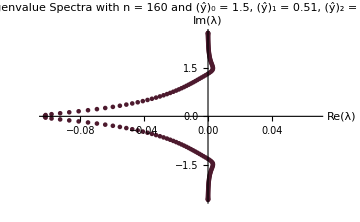
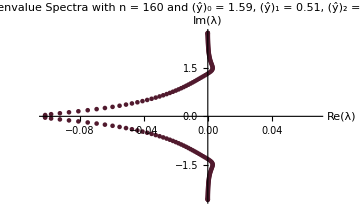
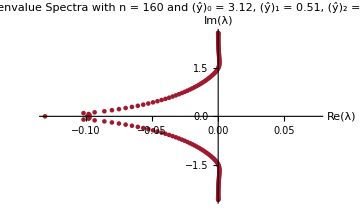
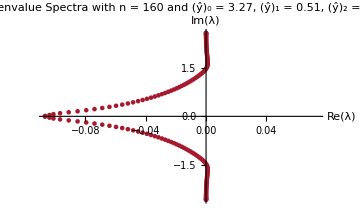
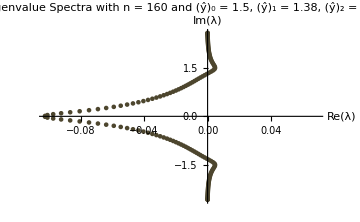
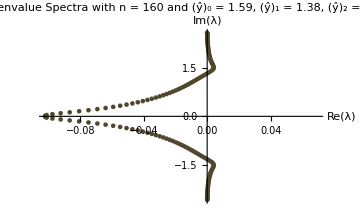
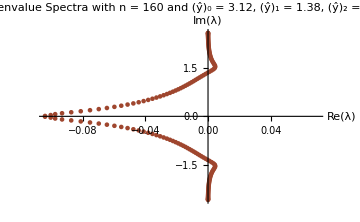
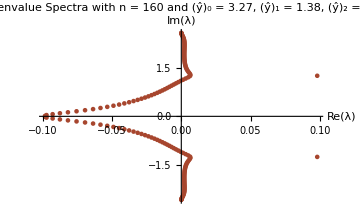

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{xx,yy,zz}];

(*Define ŷ values*)
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

(*Define ŷ values*)
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]],

{m,1,Length@stable}]
```

# B6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat3List={(*1*)2.94,(*2*)4.41};
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["P6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs1.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs2.mx"]]
ParallelEvaluate[Get["P6_bdCoeffs3.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

«2 more identical outputs»

```mathematica
DistributeDefinitions[yHat0List,yHat1List,yHat2List,yHat3List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,yHat2List,yHat3List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

Kernel 1 working on {1,1,1,1}

Kernel 2 working on {1,1,1,2}

Kernel 3 working on {1,1,1,3}

Kernel 4 working on {1,1,1,4}

Kernel 2 working on {1,1,2,1}

Kernel 4 working on {1,1,2,2}

Kernel 1 working on {1,1,2,3}

Kernel 3 working on {1,1,2,4}

Kernel 1 working on {1,1,3,1}

Kernel 4 working on {1,1,3,2}

Kernel 2 working on {1,1,3,3}

Kernel 3 working on {1,1,3,4}

Kernel 1 working on {1,1,4,1}

Kernel 2 working on {1,1,4,2}

Kernel 4 working on {1,1,4,3}

Kernel 3 working on {1,1,4,4}

Kernel 1 working on {1,2,1,1}

Kernel 2 working on {1,2,1,2}

Kernel 4 working on {1,2,1,3}

Kernel 3 working on {1,2,1,4}

Kernel 1 working on {1,2,2,1}

Kernel 2 working on {1,2,2,2}

Kernel 4 working on {1,2,2,3}

Kernel 3 working on {1,2,2,4}

Kernel 4 working on {1,2,3,1}

Kernel 1 working on {1,2,3,2}

Kernel 3 working on {1,2,3,3}

Kernel 2 working on {1,2,3,4}

Kernel 1 working on {1,2,4,1}

Kernel 4 working on {1,2,4,2}

Kernel 2 working on {1,2,4,3}

Kernel 3 working on {1,2,4,4}

Kernel 1 working on {1,3,1,1}

Kernel 3 working on {1,3,1,2}

Kernel 2 working on {1,3,1,3}

Kernel 4 working on {1,3,1,4}

Kernel 1 working on {1,3,2,1}

Kernel 3 working on {1,3,2,2}

Kernel 2 working on {1,3,2,3}

Kernel 4 working on {1,3,2,4}

Kernel 1 working on {1,3,3,1}

Kernel 3 working on {1,3,3,2}

Kernel 2 working on {1,3,3,3}

Kernel 4 working on {1,3,3,4}

Kernel 1 working on {1,3,4,1}

Kernel 3 working on {1,3,4,2}

Kernel 2 working on {1,3,4,3}

Kernel 4 working on {1,3,4,4}

Kernel 3 working on {1,4,1,1}

Kernel 1 working on {1,4,1,2}

Kernel 2 working on {1,4,1,3}

Kernel 4 working on {1,4,1,4}

Kernel 1 working on {1,4,2,1}

Kernel 3 working on {1,4,2,2}

Kernel 2 working on {1,4,2,3}

Kernel 4 working on {1,4,2,4}

Kernel 3 working on {1,4,3,1}

Kernel 1 working on {1,4,3,2}

Kernel 2 working on {1,4,3,3}

Kernel 4 working on {1,4,3,4}

Kernel 3 working on {1,4,4,1}

Kernel 1 working on {1,4,4,2}

Kernel 2 working on {1,4,4,3}

Kernel 4 working on {1,4,4,4}

Kernel 1 working on {2,1,1,1}

Kernel 3 working on {2,1,1,2}

Kernel 2 working on {2,1,1,3}

Kernel 4 working on {2,1,1,4}

Kernel 1 working on {2,1,2,1}

Kernel 3 working on {2,1,2,2}

Kernel 2 working on {2,1,2,3}

Kernel 4 working on {2,1,2,4}

Kernel 3 working on {2,1,3,1}

Kernel 1 working on {2,1,3,2}

Kernel 2 working on {2,1,3,3}

Kernel 4 working on {2,1,3,4}

Kernel 3 working on {2,1,4,1}

Kernel 1 working on {2,1,4,2}

Kernel 2 working on {2,1,4,3}

Kernel 4 working on {2,1,4,4}

Kernel 3 working on {2,2,1,1}

Kernel 1 working on {2,2,1,2}

Kernel 2 working on {2,2,1,3}

Kernel 4 working on {2,2,1,4}

Kernel 3 working on {2,2,2,1}

Kernel 1 working on {2,2,2,2}

Kernel 4 working on {2,2,2,3}

Kernel 2 working on {2,2,2,4}

Kernel 3 working on {2,2,3,1}

Kernel 1 working on {2,2,3,2}

Kernel 4 working on {2,2,3,3}

Kernel 2 working on {2,2,3,4}

Kernel 3 working on {2,2,4,1}

Kernel 1 working on {2,2,4,2}

Kernel 4 working on {2,2,4,3}

Kernel 2 working on {2,2,4,4}

Kernel 1 working on {2,3,1,1}

Kernel 3 working on {2,3,1,2}

Kernel 4 working on {2,3,1,3}

Kernel 2 working on {2,3,1,4}

Kernel 1 working on {2,3,2,1}

Kernel 3 working on {2,3,2,2}

Kernel 4 working on {2,3,2,3}

Kernel 2 working on {2,3,2,4}

Kernel 1 working on {2,3,3,1}

Kernel 4 working on {2,3,3,2}

Kernel 3 working on {2,3,3,3}

Kernel 2 working on {2,3,3,4}

Kernel 3 working on {2,3,4,1}

Kernel 4 working on {2,3,4,2}

Kernel 1 working on {2,3,4,3}

Kernel 2 working on {2,3,4,4}

Kernel 4 working on {2,4,1,1}

Kernel 3 working on {2,4,1,2}

Kernel 1 working on {2,4,1,3}

Kernel 2 working on {2,4,1,4}

Kernel 4 working on {2,4,2,1}

Kernel 3 working on {2,4,2,2}

Kernel 1 working on {2,4,2,3}

Kernel 2 working on {2,4,2,4}

Kernel 4 working on {2,4,3,1}

Kernel 3 working on {2,4,3,2}

Kernel 1 working on {2,4,3,3}

Kernel 2 working on {2,4,3,4}

Kernel 4 working on {2,4,4,1}

Kernel 3 working on {2,4,4,2}

Kernel 1 working on {2,4,4,3}

Kernel 2 working on {2,4,4,4}

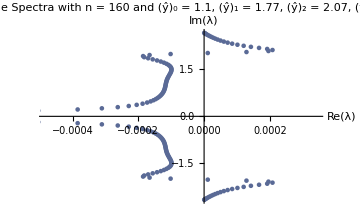
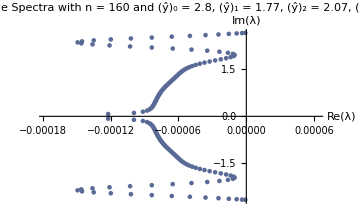
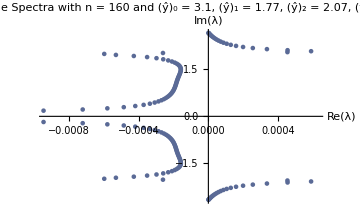
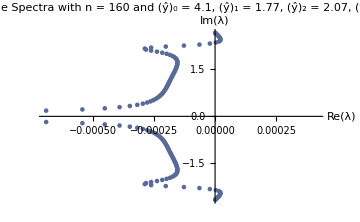
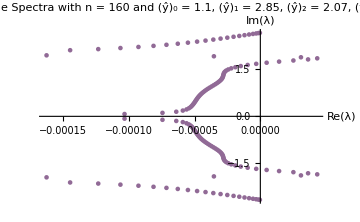
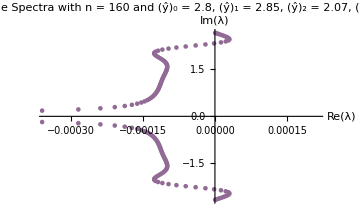
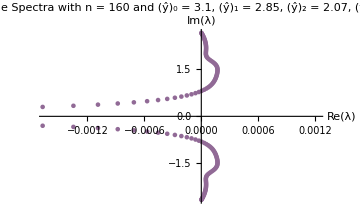
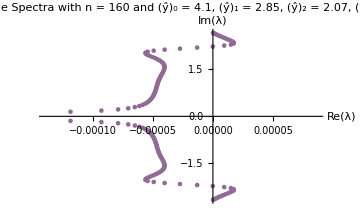
{{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}},{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}}

```mathematica
maxReList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]],yHat2List[[xx]],yHat3List[[ww]]},Max[Re[eigs]]},

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

```mathematica
DumpSave["P6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["P6_MaxReList.mx"]
maxReList
```

{{{{{{1.1,1.77,2.07,2.94},0.069282},{{2.8,1.77,2.07,2.94},0.0102496},{{3.1,1.77,2.07,2.94},0.0991029},{{4.1,1.77,2.07,2.94},0.077854}},{{{1.1,2.85,2.07,2.94},0.0000432125},{{2.8,2.85,2.07,2.94},0.0539793},{{3.1,2.85,2.07,2.94},22.1718},{{4.1,2.85,2.07,2.94},0.0232438}},{{{1.1,3.48,2.07,2.94},0.0202968},{{2.8,3.48,2.07,2.94},0.000568977},{{3.1,3.48,2.07,2.94},0.0813532},{{4.1,3.48,2.07,2.94},0.000837856}},{{{1.1,4.14,2.07,2.94},0.0000319195},{{2.8,4.14,2.07,2.94},0.0118403},{{3.1,4.14,2.07,2.94},0.396571},{{4.1,4.14,2.07,2.94},0.00655337}}},{{{{1.1,1.77,2.85,2.94},15.5254},{{2.8,1.77,2.85,2.94},55.4902},{{3.1,1.77,2.85,2.94},12.9102},{{4.1,1.77,2.85,2.94},40.0806}},{{{1.1,2.85,2.85,2.94},0.21893},{{2.8,2.85,2.85,2.94},0.148787},{{3.1,2.85,2.85,2.94},0.18897},{{4.1,2.85,2.85,2.94},0.0742782}},{{{1.1,3.48,2.85,2.94},0.359166},{{2.8,3.48,2.85,2.94},1.00758},{{3.1,3.48,2.85,2.94},0.297548},{{4.1,3.48,2.85,2.94},0.214277}},{{{1.1,4.14,2.85,2.94},0.0108779},{{2.8,4.14,2.85,2.94},0.237209},{{3.1,4.14,2.85,2.94},0.0760478},{{4.1,4.14,2.85,2.94},0.128883}}},{{{{1.1,1.77,3.9,2.94},0.989462},{{2.8,1.77,3.9,2.94},2.55475},{{3.1,1.77,3.9,2.94},13.6205},{{4.1,1.77,3.9,2.94},2.9312}},{{{1.1,2.85,3.9,2.94},0.389326},{{2.8,2.85,3.9,2.94},0.181563},{{3.1,2.85,3.9,2.94},0.121108},{{4.1,2.85,3.9,2.94},0.102817}},{{{1.1,3.48,3.9,2.94},0.477142},{{2.8,3.48,3.9,2.94},2.52963},{{3.1,3.48,3.9,2.94},0.577374},{{4.1,3.48,3.9,2.94},4.72755}},{{{1.1,4.14,3.9,2.94},1.37821},{{2.8,4.14,3.9,2.94},0.519388},{{3.1,4.14,3.9,2.94},0.31295},{{4.1,4.14,3.9,2.94},0.44367}}},{{{{1.1,1.77,4.14,2.94},4.63694},{{2.8,1.77,4.14,2.94},18.1845},{{3.1,1.77,4.14,2.94},13.2829},{{4.1,1.77,4.14,2.94},24.1897}},{{{1.1,2.85,4.14,2.94},0.306118},{{2.8,2.85,4.14,2.94},0.163241},{{3.1,2.85,4.14,2.94},0.161186},{{4.1,2.85,4.14,2.94},0.0866187}},{{{1.1,3.48,4.14,2.94},0.427903},{{2.8,3.48,4.14,2.94},7.55634},{{3.1,3.48,4.14,2.94},0.374701},{{4.1,3.48,4.14,2.94},1.29256}},{{{1.1,4.14,4.14,2.94},0.701879},{{2.8,4.14,4.14,2.94},0.258149},{{3.1,4.14,4.14,2.94},0.0368424},{{4.1,4.14,4.14,2.94},0.149135}}}},{{{{{1.1,1.77,2.07,4.41},0.0703956},{{2.8,1.77,2.07,4.41},0.0128736},{{3.1,1.77,2.07,4.41},0.0999582},{{4.1,1.77,2.07,4.41},0.0809842}},{{{1.1,2.85,2.07,4.41},0.0000318686},{{2.8,2.85,2.07,4.41},0.0545362},{{3.1,2.85,2.07,4.41},25.7494},{{4.1,2.85,2.07,4.41},0.0238922}},{{{1.1,3.48,2.07,4.41},0.0212445},{{2.8,3.48,2.07,4.41},0.000548163},{{3.1,3.48,2.07,4.41},0.0820481},{{4.1,3.48,2.07,4.41},0.000735917}},{{{1.1,4.14,2.07,4.41},0.00103068},{{2.8,4.14,2.07,4.41},0.0132674},{{3.1,4.14,2.07,4.41},0.687309},{{4.1,4.14,2.07,4.41},0.00821918}}},{{{{1.1,1.77,2.85,4.41},2.18928},{{2.8,1.77,2.85,4.41},12.6119},{{3.1,1.77,2.85,4.41},24.3686},{{4.1,1.77,2.85,4.41},15.0491}},{{{1.1,2.85,2.85,4.41},0.292085},{{2.8,2.85,2.85,4.41},0.156526},{{3.1,2.85,2.85,4.41},0.172689},{{4.1,2.85,2.85,4.41},0.0799897}},{{{1.1,3.48,2.85,4.41},0.431607},{{2.8,3.48,2.85,4.41},1.0056},{{3.1,3.48,2.85,4.41},0.348599},{{4.1,3.48,2.85,4.41},0.350537}},{{{1.1,4.14,2.85,4.41},0.00692345},{{2.8,4.14,2.85,4.41},0.65457},{{3.1,4.14,2.85,4.41},0.0571594},{{4.1,4.14,2.85,4.41},0.141441}}},{{{{1.1,1.77,3.9,4.41},6.22575},{{2.8,1.77,3.9,4.41},4.6625},{{3.1,1.77,3.9,4.41},3.38292},{{4.1,1.77,3.9,4.41},4.51491}},{{{1.1,2.85,3.9,4.41},2.86119},{{2.8,2.85,3.9,4.41},2.10449},{{3.1,2.85,3.9,4.41},1.89899},{{4.1,2.85,3.9,4.41},2.00308}},{{{1.1,3.48,3.9,4.41},2.79667},{{2.8,3.48,3.9,4.41},4.91448},{{3.1,3.48,3.9,4.41},1.04284},{{4.1,3.48,3.9,4.41},5.93513}},{{{1.1,4.14,3.9,4.41},78.576},{{2.8,4.14,3.9,4.41},2.90451},{{3.1,4.14,3.9,4.41},2.09008},{{4.1,4.14,3.9,4.41},2.66384}}},{{{{1.1,1.77,4.14,4.41},5.52279},{{2.8,1.77,4.14,4.41},67.8489},{{3.1,1.77,4.14,4.41},15.0727},{{4.1,1.77,4.14,4.41},137.678}},{{{1.1,2.85,4.14,4.41},0.944024},{{2.8,2.85,4.14,4.41},0.175329},{{3.1,2.85,4.14,4.41},0.1365},{{4.1,2.85,4.14,4.41},0.095568}},{{{1.1,3.48,4.14,4.41},1.22433},{{2.8,3.48,4.14,4.41},5.26702},{{3.1,3.48,4.14,4.41},0.482049},{{4.1,3.48,4.14,4.41},2.00791}},{{{1.1,4.14,4.14,4.41},0.349936},{{2.8,4.14,4.14,4.41},2.13219},{{3.1,4.14,4.14,4.41},0.3647},{{4.1,4.14,4.14,4.41},1.43356}}}}}

```mathematica
maxReList//TableForm
Dimensions@maxrelist
trimmed=Flatten[maxReList,2];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",{ww,xx,yy,zz}];

(*Define ŷ values*)
yHat3=yHat3List[[ww]];
yHat2=yHat2List[[xx]];
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{ww,1,Length@yHat3List},{xx,1,Length@yHat2List},{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
Print["Kernel ",$KernelID," working on ",m];

(*Define ŷ values*)
yHat3=stable[[m,1,4]];
yHat2=stable[[m,1,3]];
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsP6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]],

{m,1,Length@stable}]
```

# C6 Scheme

## Initialize Matrix and ŷ Definitions

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}];
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}];



yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};

k=160;
```

## Initialize Parallelization

```mathematica
LaunchKernels[4]
```

{Local (4),Local (4),Local (4),Local (4)}

```mathematica
ParallelEvaluate[Get["C6_interiorCoeffs.mx"]]
ParallelEvaluate[Get["C6_bdCoeffs0.mx"]]
ParallelEvaluate[Get["C6_bdCoeffs1.mx"]]
```

{Null,Null,Null,Null}

{Null,Null,Null,Null}

{Null,Null,Null,Null}

```mathematica
DistributeDefinitions[yHat0List,yHat1List,LHS,RHS,LHSRows,RHSRows,k]
```

{yHat0List,yHat1List,LHS,LHSRows,RHS,RHSRows,k}

## Run Max(Re) Test

```mathematica
maxReList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

{{yHat0List[[zz]],yHat1List[[yy]]},Max[Re[eigs]]},

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1}

Kernel 2 working on {1,2}

Kernel 3 working on {1,3}

Kernel 4 working on {1,4}

Kernel 2 working on {1,5}

Kernel 4 working on {1,6}

Kernel 3 working on {2,1}

Kernel 1 working on {2,2}

Kernel 3 working on {2,3}

Kernel 1 working on {2,4}

Kernel 2 working on {2,5}

Kernel 3 working on {2,6}

Kernel 4 working on {3,1}

Kernel 1 working on {3,2}

Kernel 3 working on {3,3}

Kernel 4 working on {3,4}

Kernel 2 working on {3,5}

Kernel 1 working on {3,6}

Kernel 3 working on {4,1}

Kernel 4 working on {4,2}

Kernel 2 working on {4,3}

Kernel 1 working on {4,4}

Kernel 4 working on {4,5}

Kernel 3 working on {4,6}

Kernel 2 working on {5,1}

Kernel 1 working on {5,2}

Kernel 4 working on {5,3}

Kernel 3 working on {5,4}

Kernel 2 working on {5,5}

Kernel 1 working on {5,6}

{{{{0.21,1.17},-0.000024486},{{0.6,1.17},0.46466},{{1.38,1.17},-4.03875×10^-6},{{1.8,1.17},-0.0000245835},{{3.12,1.17},-0.0000243222},{{3.24,1.17},10.4497}},{{{0.21,1.74},-0.0000332282},{{0.6,1.74},-0.0000374478},{{1.38,1.74},-0.0000374529},{{1.8,1.74},-0.0000318225},{{3.12,1.74},-0.0000346236},{{3.24,1.74},-0.000037469}},{{{0.21,2.31},2.00143},{{0.6,2.31},0.000883542},{{1.38,2.31},0.000885052},{{1.8,2.31},2.58392},{{3.12,2.31},1.3358},{{3.24,2.31},0.000895513}},{{{0.21,3.06},-0.0000335868},{{0.6,3.06},-0.0000372788},{{1.38,3.06},-0.0000372114},{{1.8,3.06},-0.0000330061},{{3.12,3.06},-0.0000344},{{3.24,3.06},-0.0000368957}},{{{0.21,3.51},21.9521},{{0.6,3.51},0.000875244},{{1.38,3.51},0.000799864},{{1.8,3.51},32.0849},{{3.12,3.51},14.3842},{{3.24,3.51},0.000562167}}}

```mathematica
DumpSave["C6_MaxReList.mx","Global`maxReList"];
```

## Trimming Output to find Stable Operators

```mathematica
Get["C6_MaxReList.mx"]
```

```mathematica
maxReList//TableForm
Dimensions@maxReList
trimmed=Flatten[maxReList,1];

stable={};
For[i=1,i<=Length@trimmed,i++,
If[trimmed[[i,2]]<=0,
AppendTo[stable,trimmed[[i]]]]
]
stable
Length@stable
```

0.21 | 1.17
-0.000024486 |  | 0.6 | 1.17
0.46466 |  | 1.38 | 1.17
-4.03875×10^-6 |  | 1.8 | 1.17
-0.0000245835 |  | 3.12 | 1.17
-0.0000243222 |  | 3.24 | 1.17
10.4497 | 
0.21 | 1.74
-0.0000332282 |  | 0.6 | 1.74
-0.0000374478 |  | 1.38 | 1.74
-0.0000374529 |  | 1.8 | 1.74
-0.0000318225 |  | 3.12 | 1.74
-0.0000346236 |  | 3.24 | 1.74
-0.000037469 | 
0.21 | 2.31
2.00143 |  | 0.6 | 2.31
0.000883542 |  | 1.38 | 2.31
0.000885052 |  | 1.8 | 2.31
2.58392 |  | 3.12 | 2.31
1.3358 |  | 3.24 | 2.31
0.000895513 | 
0.21 | 3.06
-0.0000335868 |  | 0.6 | 3.06
-0.0000372788 |  | 1.38 | 3.06
-0.0000372114 |  | 1.8 | 3.06
-0.0000330061 |  | 3.12 | 3.06
-0.0000344 |  | 3.24 | 3.06
-0.0000368957 | 
0.21 | 3.51
21.9521 |  | 0.6 | 3.51
0.000875244 |  | 1.38 | 3.51
0.000799864 |  | 1.8 | 3.51
32.0849 |  | 3.12 | 3.51
14.3842 |  | 3.24 | 3.51
0.000562167 |

{5,6,2}

{{{0.21,1.17},-0.000024486},{{1.38,1.17},-4.03875×10^-6},{{1.8,1.17},-0.0000245835},{{3.12,1.17},-0.0000243222},{{0.21,1.74},-0.0000332282},{{0.6,1.74},-0.0000374478},{{1.38,1.74},-0.0000374529},{{1.8,1.74},-0.0000318225},{{3.12,1.74},-0.0000346236},{{3.24,1.74},-0.000037469},{{0.21,3.06},-0.0000335868},{{0.6,3.06},-0.0000372788},{{1.38,3.06},-0.0000372114},{{1.8,3.06},-0.0000330061},{{3.12,3.06},-0.0000344},{{3.24,3.06},-0.0000368957}}

16

## Run Eigenvalue Spectra on All Operators

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",{yy,zz}];*)

(*Define ŷ values*)
yHat1=yHat1List[[yy]];
yHat0=yHat0List[[zz]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{yy,1,Length@yHat1List},{zz,1,Length@yHat0List}]
```

Kernel 1 working on {1,1}

Kernel 2 working on {1,2}

Kernel 3 working on {1,3}

Kernel 4 working on {1,4}

Kernel 2 working on {1,5}

Kernel 3 working on {1,6}

Kernel 4 working on {2,1}

Kernel 1 working on {2,2}

Kernel 2 working on {2,3}

Kernel 3 working on {2,4}

Kernel 1 working on {2,5}

Kernel 4 working on {2,6}

Kernel 2 working on {3,1}

Kernel 3 working on {3,2}

Kernel 4 working on {3,3}

Kernel 1 working on {3,4}

Kernel 2 working on {3,5}

Kernel 1 working on {3,6}

Kernel 3 working on {4,1}

Kernel 4 working on {4,2}

Kernel 2 working on {4,3}

Kernel 4 working on {4,4}

Kernel 1 working on {4,5}

Kernel 3 working on {4,6}

Kernel 2 working on {5,1}

Kernel 4 working on {5,2}

Kernel 1 working on {5,3}

Kernel 3 working on {5,4}

Kernel 2 working on {5,5}

Kernel 4 working on {5,6}

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

## Run Eigenvalue Spectra on Stable Operators Only

```mathematica
eigSpectraList=ParallelTable[
(*Print["Kernel ",$KernelID," working on ",m];*)

(*Define ŷ values*)
yHat1=stable[[m,1,2]];
yHat0=stable[[m,1,1]];



(*Coefficient Definition*)
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};



(*Coefficient Formatting*)
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]];



(*Modified Boundary Coefficients*)
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1];



(*Eigenvalue Analysis*)
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]],

{m,1,Length@stable}]
```

Kernel 1 working on 1

Kernel 2 working on 3

Kernel 3 working on 5

Kernel 4 working on 7

Kernel 3 working on 6

Kernel 4 working on 8

Kernel 1 working on 2

Kernel 2 working on 4

Kernel 4 working on 9

Kernel 2 working on 11

Kernel 1 working on 13

Kernel 3 working on 15

Kernel 4 working on 10

Kernel 2 working on 12

Kernel 3 working on 16

Kernel 1 working on 14

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}